```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileNames[]
```

{2017-04-05_v3 (1).nb,final-NG-1200-100SK-27BTDC.pdf,NG-1200-100SK-27BTDC.TXT,NG-1400-100SK-27BTDC.TXT,NG-1500-100SK-27BTDC.TXT,NG-1600-100SK-27BTDC.TXT,NG-1800-100SK-27BTDC.TXT,NG-2000-100SK-27BTDC.TXT,piatystlpec-NG-1200-100SK-27BTDC.TXT.txt,piatystlpec-NG-1200-100SK-27BTDC.TXT.xls,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.txt,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.xls,tretistlpec-NG-1200-100SK-27BTDC.TXT.txt,tretistlpec-NG-1200-100SK-27BTDC.TXT.xls}

definujeme subor

```mathematica
subor="NG-1200-100SK-27BTDC.TXT";
```

```mathematica
n=ReadList[subor,Table[Number,{5}]];
```

```mathematica
prvystlpec=n[[All,1]];
druhystlpec=n[[All,2]];
tretistlpec=n[[All,3]];
stvrtystlpec=n[[All,4]];
piatystlpec=n[[All,5]];
```

nakreslíme si jednotlivé stĺpce

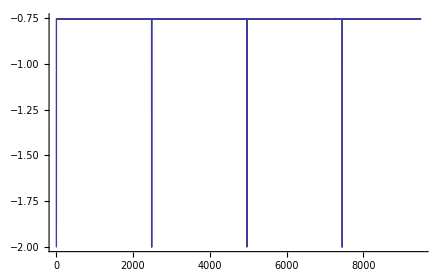

```mathematica
ListLinePlot[druhystlpec[[1;;9500;;1]],PlotRange->All]
```

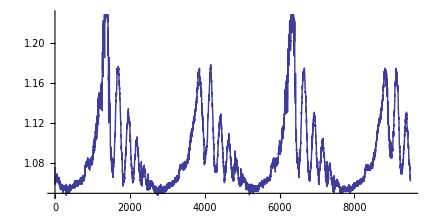

```mathematica
ListLinePlot[tretistlpec[[1;;9500;;1]],AspectRatio->0.5]
```

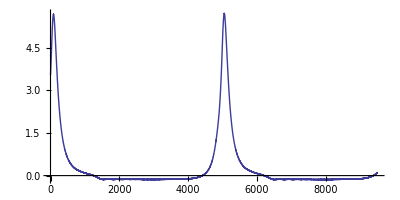

```mathematica
ListLinePlot[stvrtystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

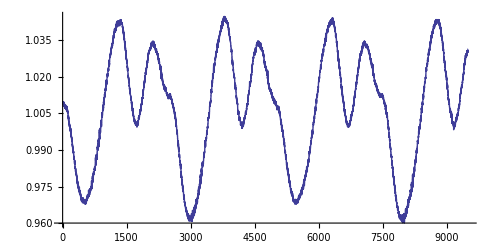

```mathematica
ListLinePlot[piatystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

```mathematica
Length[prvystlpec]
```

1045980

Zistíme, kde sú hranice jednotlivých cyklov a pretože niekedy máme niekoľko hodnôt okolo -2, tak necháme len jednu referenčnú a ostatné odstránime
Musíme to tak spraviť, lebo keby sme to nespravli tak pri počítaní priemerov by sme nedostali správne hodnoty, ale hodnoty by boli vzájomne posunuté - čiže by sme mali na houby výsledok

```mathematica
pom3={};
Do[
If[druhystlpec[[i]]<-1.8,AppendTo[pom3, i]],{i,1,Length[druhystlpec]}];
pom4={};
Do[
If[pom3[[i+1]]-pom3[[i]]>10,AppendTo[pom4,pom3[[i]]]],{i,1, Length[pom3]-1}];
pom4
```

{2,2486,4968,7452,9934,12417,14899,17383,19865,22349,24830,27315,29796,32279,34760,37244,39725,42208,44689,47172,49653,52136,54617,57100,59581,62065,64546,67030,69511,71994,74475,76958,79439,81921,84401,86883,89363,91845,94325,96806,99285,101767,104247,106728,109208,111690,114170,116653,119134,121618,124099,126583,129066,131550,134032,136516,138997,141482,143964,146448,148930,151415,153897,156381,158864,161348,163831,166315,168799,171284,173768,176253,178737,181223,183706,186193,188676,191162,193645,196131,198613,201097,203579,206063,208544,211028,213509,215992,218473,220956,223437,225919,228400,230884,233364,235847,238327,240810,243290,245773,248253,250736,253216,255699,258182,260665,263148,265632,268115,270601,273084,275568,278051,280535,283017,285502,287985,290470,292952,295436,297918,300401,302883,305366,307847,310331,312812,315295,317777,320261,322743,325226,327708,330191,332672,335157,337639,340124,342607,345093,347577,350063,352546,355032,357515,359999,362481,364965,367446,369931,372412,374896,377378,379862,382343,384828,387311,389795,392276,394759,397240,399723,402203,404685,407165,409648,412127,414609,417089,419571,422050,424531,427011,429493,431973,434455,436936,439418,441898,444381,446862,449345,451827,454309,456791,459274,461756,464240,466722,469206,471689,474173,476655,479140,481623,484107,486589,489072,491554,494037,496518,499001,501482,503966,506447,508931,511413,513897,516379,518863,521345,523828,526310,528793,531275,533758,536240,538724,541206,543690,546172,548656,551139,553625,556107,558591,561074,563558,566040,568524,571006,573491,575973,578457,580939,583423,585904,588387,590868,593351,595831,598313,600794,603275,605756,608239,610720,613203,615685,618169,620650,623134,625616,628100,630581,633065,635547,638031,640513,642996,645478,647962,650443,652927,655408,657892,660374,662858,665340,667824,670306,672790,675272,677757,680239,682722,685204,687687,690168,692650,695131,697614,700095,702578,705058,707541,710022,712504,714985,717468,719949,722432,724914,727398,729880,732364,734846,737330,739813,742298,744781,747266,749751,752236,754720,757205,759689,762173,764656,767141,769624,772109,774591,777075,779557,782041,784523,787008,789490,791974,794456,796940,799422,801906,804388,806872,809353,811837,814319,816802,819283,821768,824250,826734,829216,831700,834182,836667,839148,841632,844113,846596,849078,851562,854044,856527,859008,861493,863974,866458,868940,871425,873907,876392,878873,881357,883839,886323,888805,891289,893771,896255,898736,901220,903702,906186,908668,911151,913633,916117,918598,921081,923562,926044,928525,931008,933490,935973,938453,940937,943418,945901,948382,950865,953346,955829,958310,960793,963275,965758,968239,970721,973202,975685,978166,980649,983130,985614,988095,990578,993060,995543,998024,1000508,1002989,1005473,1007956,1010440,1012922,1015407,1017889,1020373,1022854,1025338,1027819,1030302,1032783,1035267,1037748,1040232,1042714}

```mathematica
Length[pom4]
```

421

rozsekáme celé dáta na jednotlivé cykly

```mathematica
cyklus={};
Table[AppendTo[cyklus,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus//Length
```

209

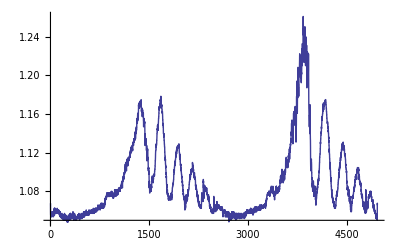
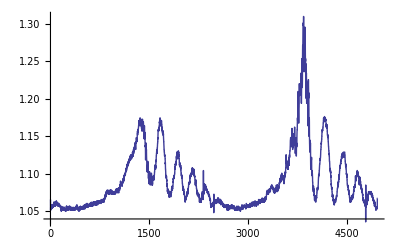
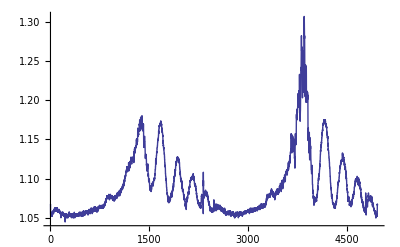
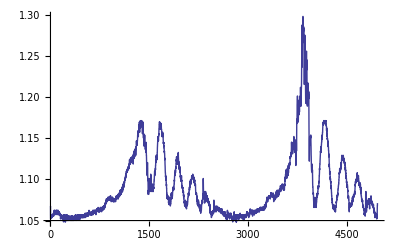
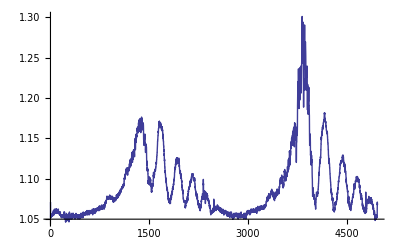
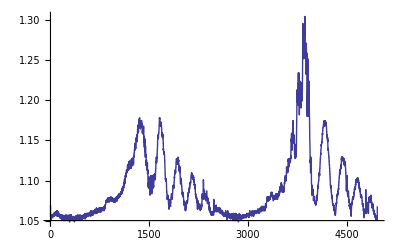
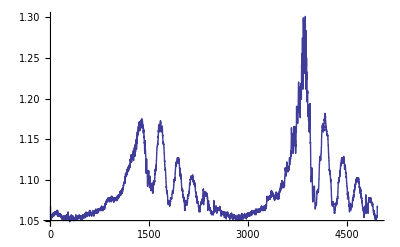
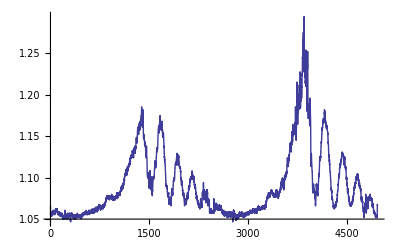

```mathematica
Table[ListLinePlot[cyklus[[i]],PlotRange->All],{i,1,10}]
```

toto sú dĺžky jednotlivých cyklov - vidíme, že sú podobné, ale nie sú rovnaké - takže ich zosúladíme

```mathematica
Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]
```

{4967,4966,4967,4967,4967,4965,4966,4965,4965,4965,4965,4966,4966,4965,4965,4964,4963,4963,4962,4962,4962,4963,4964,4966,4966,4968,4967,4967,4967,4968,4967,4968,4968,4970,4970,4971,4971,4970,4970,4967,4967,4966,4965,4965,4964,4966,4964,4964,4964,4964,4964,4967,4968,4970,4968,4968,4968,4969,4967,4966,4966,4966,4965,4967,4966,4966,4967,4968,4970,4971,4970,4968,4967,4967,4966,4967,4967,4968,4965,4965,4963,4964,4962,4963,4961,4963,4963,4964,4964,4965,4965,4966,4967,4967,4968,4968,4968,4966,4966,4965,4966,4966,4967,4967,4966,4966,4966,4967,4967,4967,4970,4967,4968,4967,4968,4967,4967,4965,4965,4963,4963,4965,4965,4967,4966,4967,4966,4967,4966,4967,4966,4966,4967,4967,4967,4968,4966,4966,4964,4965,4965,4964,4964,4965,4965,4967,4967,4967,4969,4969,4971,4970,4969,4969,4969,4967,4967,4968,4967,4967,4967,4967,4966,4966,4967,4967,4967,4968,4966,4965,4967,4966,4967,4966,4968,4968,4966,4967,4967,4967,4966,4967,4966,4967,4965,4964,4965,4966,4965,4965,4965,4965,4965,4966,4964,4965,4965,4966,4965,4966,4966,4966,4968,4968,4967,4966,4965,4966,4966}

```mathematica
pom5=Min[Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]];
pom6=Table[Take[cyklus[[i]],pom5],{i,1,Length[cyklus]}];
```

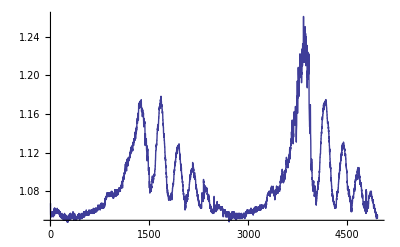
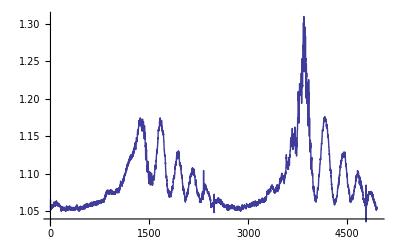
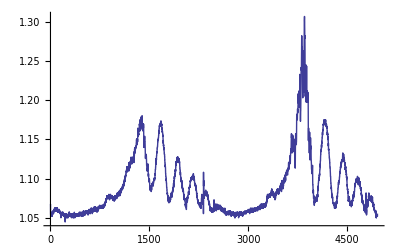
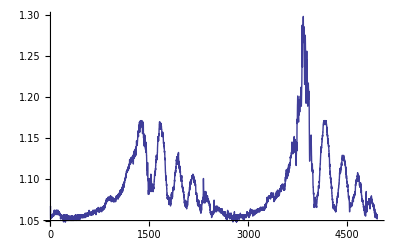
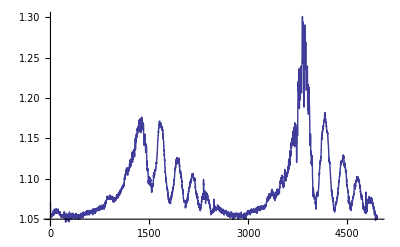
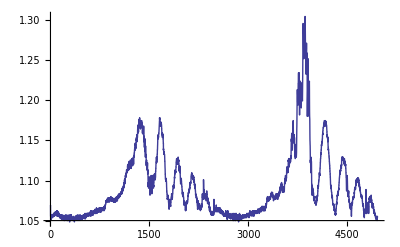
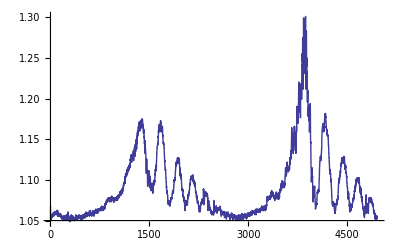
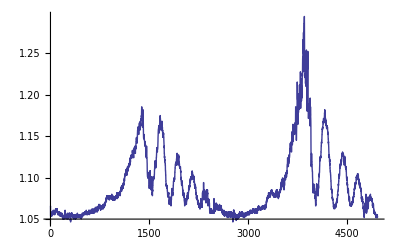

```mathematica
Table[ListLinePlot[pom6[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[pom6]//Dimensions
```

{4961,209}

nakreslíme si jednotlivé stĺpce a prepočítame to na priemer vo všetkých nameraných cykloch

```mathematica
priemernehodnotydruhystlpec=Table[Mean[pom6[[All,i]]],{i,1,4961}];
```

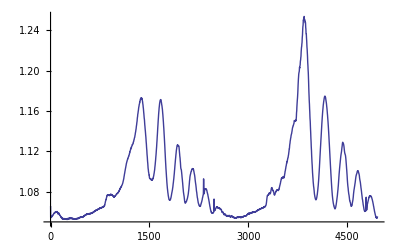

```mathematica
ListLinePlot[priemernehodnotydruhystlpec]
```

to isté spravíme pre všetky ostatné stĺpce

```mathematica
cyklus3={};
cyklus4={};
cyklus5={};
Table[AppendTo[cyklus3,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus4,stvrtystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus5,piatystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus3//Length
```

209

```mathematica
Table[ListLinePlot[cyklus3[[i]],PlotRange->All],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

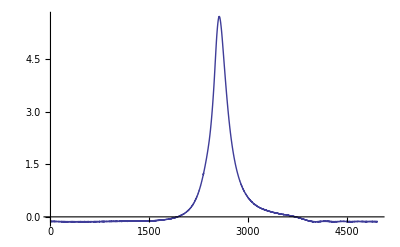
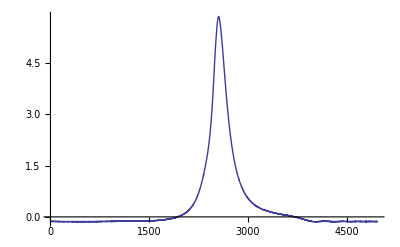
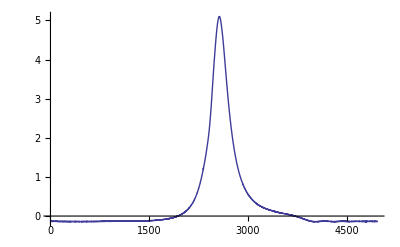
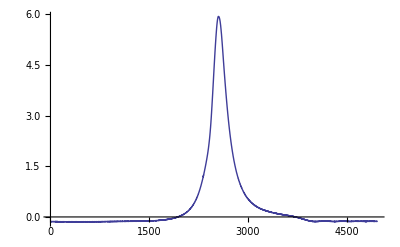
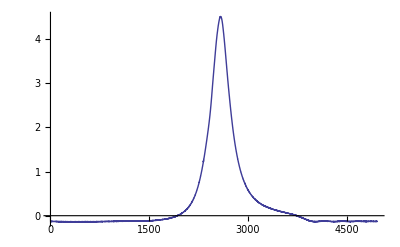
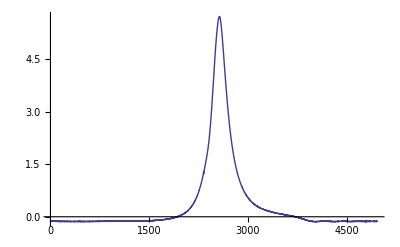
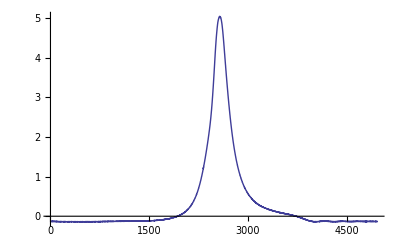
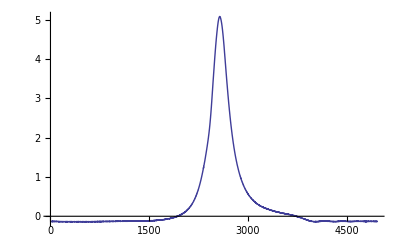

```mathematica
Table[ListLinePlot[cyklus4[[i]],PlotRange->All],{i,1,10}]
```

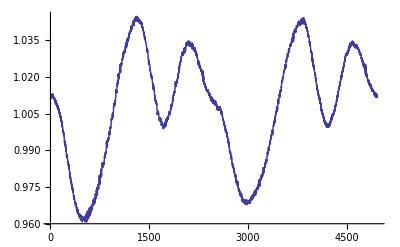
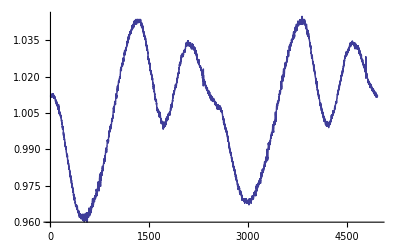
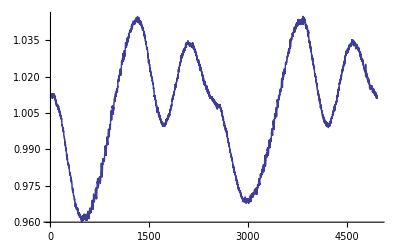
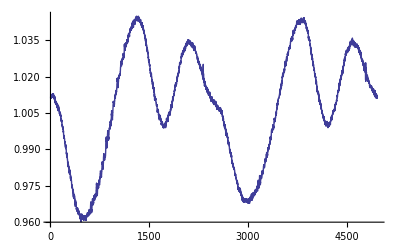
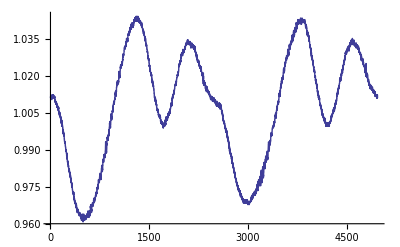
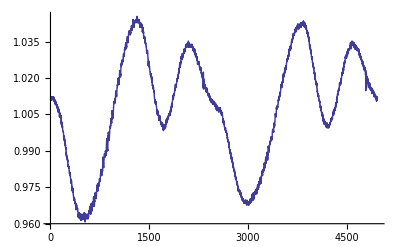
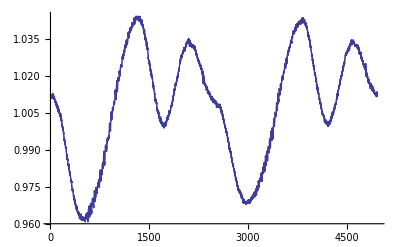
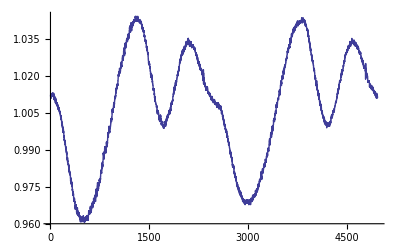

```mathematica
Table[ListLinePlot[cyklus5[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus3[[i]]],{i,1,Length[cyklus]}]
```

{4967,4966,4967,4967,4967,4965,4966,4965,4965,4965,4965,4966,4966,4965,4965,4964,4963,4963,4962,4962,4962,4963,4964,4966,4966,4968,4967,4967,4967,4968,4967,4968,4968,4970,4970,4971,4971,4970,4970,4967,4967,4966,4965,4965,4964,4966,4964,4964,4964,4964,4964,4967,4968,4970,4968,4968,4968,4969,4967,4966,4966,4966,4965,4967,4966,4966,4967,4968,4970,4971,4970,4968,4967,4967,4966,4967,4967,4968,4965,4965,4963,4964,4962,4963,4961,4963,4963,4964,4964,4965,4965,4966,4967,4967,4968,4968,4968,4966,4966,4965,4966,4966,4967,4967,4966,4966,4966,4967,4967,4967,4970,4967,4968,4967,4968,4967,4967,4965,4965,4963,4963,4965,4965,4967,4966,4967,4966,4967,4966,4967,4966,4966,4967,4967,4967,4968,4966,4966,4964,4965,4965,4964,4964,4965,4965,4967,4967,4967,4969,4969,4971,4970,4969,4969,4969,4967,4967,4968,4967,4967,4967,4967,4966,4966,4967,4967,4967,4968,4966,4965,4967,4966,4967,4966,4968,4968,4966,4967,4967,4967,4966,4967,4966,4967,4965,4964,4965,4966,4965,4965,4965,4965,4965,4966,4964,4965,4965,4966,4965,4966,4966,4966,4968,4968,4967,4966,4965,4966,4966}

```mathematica
pom5=Min[Table[Length[cyklus3[[i]]],{i,1,Length[cyklus3]}]];
cyklus3orezany=Table[Take[cyklus3[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus4orezany=Table[Take[cyklus4[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus5orezany=Table[Take[cyklus5[[i]],pom5],{i,1,Length[cyklus3]}];
```

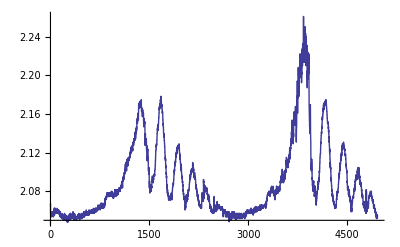
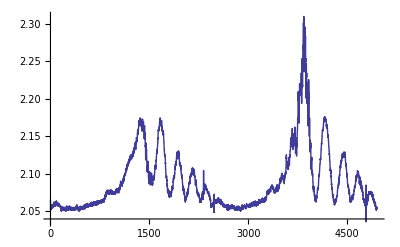
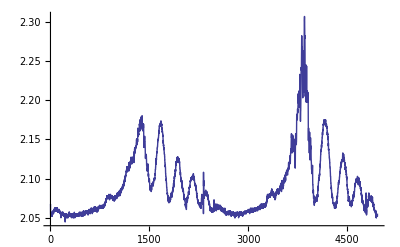
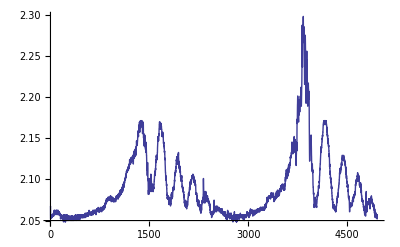
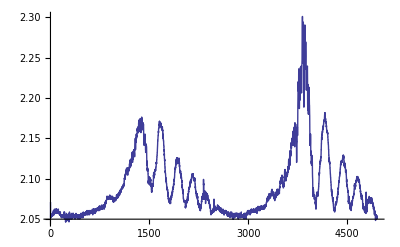
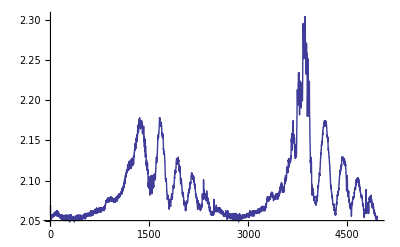
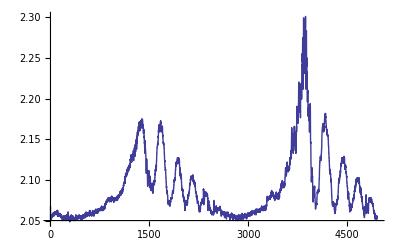
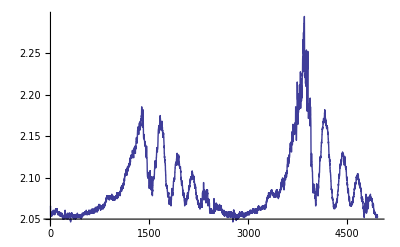

```mathematica
Table[ListLinePlot[cyklus3orezany[[i]]+1,PlotRange->All],{i,1,10}]
```

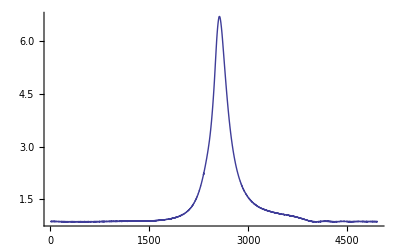
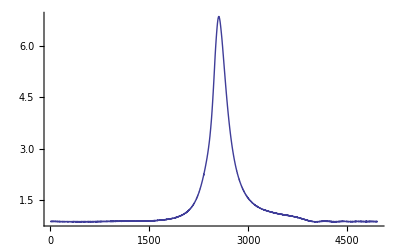
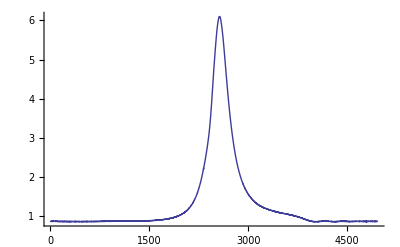
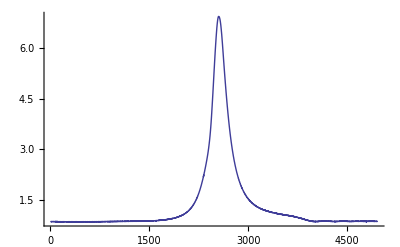
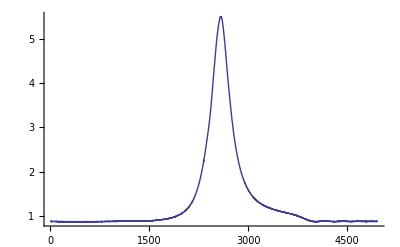
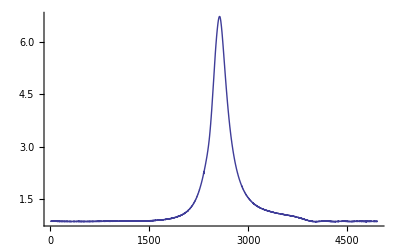
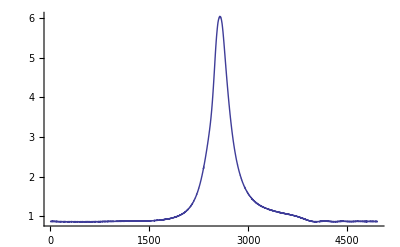
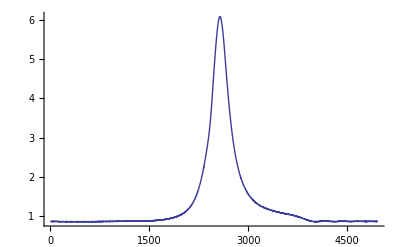

```mathematica
Table[ListLinePlot[cyklus4orezany[[i]]+1,PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[cyklus3orezany]//Dimensions
```

{4961,209}

```mathematica
priemernehodnoty3stlpec=Table[Mean[cyklus3orezany[[All,i]]],{i,1,4961}];
priemernehodnoty4stlpec=Table[Mean[cyklus4orezany[[All,i]]],{i,1,4961}];
priemernehodnoty5stlpec=Table[Mean[cyklus5orezany[[All,i]]],{i,1,4961}];
```

a možeme sa graficky vytešovať

```mathematica
Length[priemernehodnoty4stlpec]
```

4961

```mathematica
k=0;
x=Table[k=k+720/Length[priemernehodnoty4stlpec]//N,{Length[priemernehodnoty4stlpec]}];
Print[x]
```

{0.145132,0.290264,0.435396,0.580528,0.72566,0.870792,1.01592,1.16106,1.30619,1.45132,1.59645,1.74158,1.88672,2.03185,2.17698,2.32211,2.46724,2.61238,2.75751,2.90264,3.04777,3.1929,3.33804,3.48317,3.6283,3.77343,3.91856,4.0637,4.20883,4.35396,4.49909,4.64422,4.78936,4.93449,5.07962,5.22475,5.36989,5.51502,5.66015,5.80528,5.95041,6.09555,6.24068,6.38581,6.53094,6.67607,6.82121,6.96634,7.11147,7.2566,7.40173,7.54687,7.692,7.83713,7.98226,8.12739,8.27253,8.41766,8.56279,8.70792,8.85305,8.99819,9.14332,9.28845,9.43358,9.57871,9.72385,9.86898,10.0141,10.1592,10.3044,10.4495,10.5946,10.7398,10.8849,11.03,11.1752,11.3203,11.4654,11.6106,11.7557,11.9008,12.046,12.1911,12.3362,12.4814,12.6265,12.7716,12.9168,13.0619,13.207,13.3521,13.4973,13.6424,13.7875,13.9327,14.0778,14.2229,14.3681,14.5132,14.6583,14.8035,14.9486,15.0937,15.2389,15.384,15.5291,15.6743,15.8194,15.9645,16.1097,16.2548,16.3999,16.5451,16.6902,16.8353,16.9804,17.1256,17.2707,17.4158,17.561,17.7061,17.8512,17.9964,18.1415,18.2866,18.4318,18.5769,18.722,18.8672,19.0123,19.1574,19.3026,19.4477,19.5928,19.738,19.8831,20.0282,20.1734,20.3185,20.4636,20.6087,20.7539,20.899,21.0441,21.1893,21.3344,21.4795,21.6247,21.7698,21.9149,22.0601,22.2052,22.3503,22.4955,22.6406,22.7857,22.9309,23.076,23.2211,23.3663,23.5114,23.6565,23.8017,23.9468,24.0919,24.237,24.3822,24.5273,24.6724,24.8176,24.9627,25.1078,25.253,25.3981,25.5432,25.6884,25.8335,25.9786,26.1238,26.2689,26.414,26.5592,26.7043,26.8494,26.9946,27.1397,27.2848,27.43,27.5751,27.7202,27.8653,28.0105,28.1556,28.3007,28.4459,28.591,28.7361,28.8813,29.0264,29.1715,29.3167,29.4618,29.6069,29.7521,29.8972,30.0423,30.1875,30.3326,30.4777,30.6229,30.768,30.9131,31.0583,31.2034,31.3485,31.4937,31.6388,31.7839,31.929,32.0742,32.2193,32.3644,32.5096,32.6547,32.7998,32.945,33.0901,33.2352,33.3804,33.5255,33.6706,33.8158,33.9609,34.106,34.2512,34.3963,34.5414,34.6866,34.8317,34.9768,35.122,35.2671,35.4122,35.5573,35.7025,35.8476,35.9927,36.1379,36.283,36.4281,36.5733,36.7184,36.8635,37.0087,37.1538,37.2989,37.4441,37.5892,37.7343,37.8795,38.0246,38.1697,38.3149,38.46,38.6051,38.7503,38.8954,39.0405,39.1856,39.3308,39.4759,39.621,39.7662,39.9113,40.0564,40.2016,40.3467,40.4918,40.637,40.7821,40.9272,41.0724,41.2175,41.3626,41.5078,41.6529,41.798,41.9432,42.0883,42.2334,42.3786,42.5237,42.6688,42.8139,42.9591,43.1042,43.2493,43.3945,43.5396,43.6847,43.8299,43.975,44.1201,44.2653,44.4104,44.5555,44.7007,44.8458,44.9909,45.1361,45.2812,45.4263,45.5715,45.7166,45.8617,46.0069,46.152,46.2971,46.4422,46.5874,46.7325,46.8776,47.0228,47.1679,47.313,47.4582,47.6033,47.7484,47.8936,48.0387,48.1838,48.329,48.4741,48.6192,48.7644,48.9095,49.0546,49.1998,49.3449,49.49,49.6352,49.7803,49.9254,50.0706,50.2157,50.3608,50.5059,50.6511,50.7962,50.9413,51.0865,51.2316,51.3767,51.5219,51.667,51.8121,51.9573,52.1024,52.2475,52.3927,52.5378,52.6829,52.8281,52.9732,53.1183,53.2635,53.4086,53.5537,53.6989,53.844,53.9891,54.1342,54.2794,54.4245,54.5696,54.7148,54.8599,55.005,55.1502,55.2953,55.4404,55.5856,55.7307,55.8758,56.021,56.1661,56.3112,56.4564,56.6015,56.7466,56.8918,57.0369,57.182,57.3272,57.4723,57.6174,57.7625,57.9077,58.0528,58.1979,58.3431,58.4882,58.6333,58.7785,58.9236,59.0687,59.2139,59.359,59.5041,59.6493,59.7944,59.9395,60.0847,60.2298,60.3749,60.5201,60.6652,60.8103,60.9555,61.1006,61.2457,61.3908,61.536,61.6811,61.8262,61.9714,62.1165,62.2616,62.4068,62.5519,62.697,62.8422,62.9873,63.1324,63.2776,63.4227,63.5678,63.713,63.8581,64.0032,64.1484,64.2935,64.4386,64.5838,64.7289,64.874,65.0191,65.1643,65.3094,65.4545,65.5997,65.7448,65.8899,66.0351,66.1802,66.3253,66.4705,66.6156,66.7607,66.9059,67.051,67.1961,67.3413,67.4864,67.6315,67.7767,67.9218,68.0669,68.2121,68.3572,68.5023,68.6475,68.7926,68.9377,69.0828,69.228,69.3731,69.5182,69.6634,69.8085,69.9536,70.0988,70.2439,70.389,70.5342,70.6793,70.8244,70.9696,71.1147,71.2598,71.405,71.5501,71.6952,71.8404,71.9855,72.1306,72.2758,72.4209,72.566,72.7111,72.8563,73.0014,73.1465,73.2917,73.4368,73.5819,73.7271,73.8722,74.0173,74.1625,74.3076,74.4527,74.5979,74.743,74.8881,75.0333,75.1784,75.3235,75.4687,75.6138,75.7589,75.9041,76.0492,76.1943,76.3394,76.4846,76.6297,76.7748,76.92,77.0651,77.2102,77.3554,77.5005,77.6456,77.7908,77.9359,78.081,78.2262,78.3713,78.5164,78.6616,78.8067,78.9518,79.097,79.2421,79.3872,79.5324,79.6775,79.8226,79.9677,80.1129,80.258,80.4031,80.5483,80.6934,80.8385,80.9837,81.1288,81.2739,81.4191,81.5642,81.7093,81.8545,81.9996,82.1447,82.2899,82.435,82.5801,82.7253,82.8704,83.0155,83.1607,83.3058,83.4509,83.596,83.7412,83.8863,84.0314,84.1766,84.3217,84.4668,84.612,84.7571,84.9022,85.0474,85.1925,85.3376,85.4828,85.6279,85.773,85.9182,86.0633,86.2084,86.3536,86.4987,86.6438,86.789,86.9341,87.0792,87.2243,87.3695,87.5146,87.6597,87.8049,87.95,88.0951,88.2403,88.3854,88.5305,88.6757,88.8208,88.9659,89.1111,89.2562,89.4013,89.5465,89.6916,89.8367,89.9819,90.127,90.2721,90.4173,90.5624,90.7075,90.8527,90.9978,91.1429,91.288,91.4332,91.5783,91.7234,91.8686,92.0137,92.1588,92.304,92.4491,92.5942,92.7394,92.8845,93.0296,93.1748,93.3199,93.465,93.6102,93.7553,93.9004,94.0456,94.1907,94.3358,94.481,94.6261,94.7712,94.9163,95.0615,95.2066,95.3517,95.4969,95.642,95.7871,95.9323,96.0774,96.2225,96.3677,96.5128,96.6579,96.8031,96.9482,97.0933,97.2385,97.3836,97.5287,97.6739,97.819,97.9641,98.1093,98.2544,98.3995,98.5446,98.6898,98.8349,98.98,99.1252,99.2703,99.4154,99.5606,99.7057,99.8508,99.996,100.141,100.286,100.431,100.576,100.722,100.867,101.012,101.157,101.302,101.447,101.592,101.738,101.883,102.028,102.173,102.318,102.463,102.608,102.753,102.899,103.044,103.189,103.334,103.479,103.624,103.769,103.915,104.06,104.205,104.35,104.495,104.64,104.785,104.93,105.076,105.221,105.366,105.511,105.656,105.801,105.946,106.092,106.237,106.382,106.527,106.672,106.817,106.962,107.107,107.253,107.398,107.543,107.688,107.833,107.978,108.123,108.268,108.414,108.559,108.704,108.849,108.994,109.139,109.284,109.43,109.575,109.72,109.865,110.01,110.155,110.3,110.445,110.591,110.736,110.881,111.026,111.171,111.316,111.461,111.607,111.752,111.897,112.042,112.187,112.332,112.477,112.622,112.768,112.913,113.058,113.203,113.348,113.493,113.638,113.784,113.929,114.074,114.219,114.364,114.509,114.654,114.799,114.945,115.09,115.235,115.38,115.525,115.67,115.815,115.96,116.106,116.251,116.396,116.541,116.686,116.831,116.976,117.122,117.267,117.412,117.557,117.702,117.847,117.992,118.137,118.283,118.428,118.573,118.718,118.863,119.008,119.153,119.299,119.444,119.589,119.734,119.879,120.024,120.169,120.314,120.46,120.605,120.75,120.895,121.04,121.185,121.33,121.476,121.621,121.766,121.911,122.056,122.201,122.346,122.491,122.637,122.782,122.927,123.072,123.217,123.362,123.507,123.652,123.798,123.943,124.088,124.233,124.378,124.523,124.668,124.814,124.959,125.104,125.249,125.394,125.539,125.684,125.829,125.975,126.12,126.265,126.41,126.555,126.7,126.845,126.991,127.136,127.281,127.426,127.571,127.716,127.861,128.006,128.152,128.297,128.442,128.587,128.732,128.877,129.022,129.168,129.313,129.458,129.603,129.748,129.893,130.038,130.183,130.329,130.474,130.619,130.764,130.909,131.054,131.199,131.344,131.49,131.635,131.78,131.925,132.07,132.215,132.36,132.506,132.651,132.796,132.941,133.086,133.231,133.376,133.521,133.667,133.812,133.957,134.102,134.247,134.392,134.537,134.683,134.828,134.973,135.118,135.263,135.408,135.553,135.698,135.844,135.989,136.134,136.279,136.424,136.569,136.714,136.86,137.005,137.15,137.295,137.44,137.585,137.73,137.875,138.021,138.166,138.311,138.456,138.601,138.746,138.891,139.036,139.182,139.327,139.472,139.617,139.762,139.907,140.052,140.198,140.343,140.488,140.633,140.778,140.923,141.068,141.213,141.359,141.504,141.649,141.794,141.939,142.084,142.229,142.375,142.52,142.665,142.81,142.955,143.1,143.245,143.39,143.536,143.681,143.826,143.971,144.116,144.261,144.406,144.552,144.697,144.842,144.987,145.132,145.277,145.422,145.567,145.713,145.858,146.003,146.148,146.293,146.438,146.583,146.728,146.874,147.019,147.164,147.309,147.454,147.599,147.744,147.89,148.035,148.18,148.325,148.47,148.615,148.76,148.905,149.051,149.196,149.341,149.486,149.631,149.776,149.921,150.067,150.212,150.357,150.502,150.647,150.792,150.937,151.082,151.228,151.373,151.518,151.663,151.808,151.953,152.098,152.243,152.389,152.534,152.679,152.824,152.969,153.114,153.259,153.405,153.55,153.695,153.84,153.985,154.13,154.275,154.42,154.566,154.711,154.856,155.001,155.146,155.291,155.436,155.582,155.727,155.872,156.017,156.162,156.307,156.452,156.597,156.743,156.888,157.033,157.178,157.323,157.468,157.613,157.759,157.904,158.049,158.194,158.339,158.484,158.629,158.774,158.92,159.065,159.21,159.355,159.5,159.645,159.79,159.935,160.081,160.226,160.371,160.516,160.661,160.806,160.951,161.097,161.242,161.387,161.532,161.677,161.822,161.967,162.112,162.258,162.403,162.548,162.693,162.838,162.983,163.128,163.274,163.419,163.564,163.709,163.854,163.999,164.144,164.289,164.435,164.58,164.725,164.87,165.015,165.16,165.305,165.451,165.596,165.741,165.886,166.031,166.176,166.321,166.466,166.612,166.757,166.902,167.047,167.192,167.337,167.482,167.627,167.773,167.918,168.063,168.208,168.353,168.498,168.643,168.789,168.934,169.079,169.224,169.369,169.514,169.659,169.804,169.95,170.095,170.24,170.385,170.53,170.675,170.82,170.966,171.111,171.256,171.401,171.546,171.691,171.836,171.981,172.127,172.272,172.417,172.562,172.707,172.852,172.997,173.143,173.288,173.433,173.578,173.723,173.868,174.013,174.158,174.304,174.449,174.594,174.739,174.884,175.029,175.174,175.319,175.465,175.61,175.755,175.9,176.045,176.19,176.335,176.481,176.626,176.771,176.916,177.061,177.206,177.351,177.496,177.642,177.787,177.932,178.077,178.222,178.367,178.512,178.658,178.803,178.948,179.093,179.238,179.383,179.528,179.673,179.819,179.964,180.109,180.254,180.399,180.544,180.689,180.835,180.98,181.125,181.27,181.415,181.56,181.705,181.85,181.996,182.141,182.286,182.431,182.576,182.721,182.866,183.011,183.157,183.302,183.447,183.592,183.737,183.882,184.027,184.173,184.318,184.463,184.608,184.753,184.898,185.043,185.188,185.334,185.479,185.624,185.769,185.914,186.059,186.204,186.35,186.495,186.64,186.785,186.93,187.075,187.22,187.365,187.511,187.656,187.801,187.946,188.091,188.236,188.381,188.527,188.672,188.817,188.962,189.107,189.252,189.397,189.542,189.688,189.833,189.978,190.123,190.268,190.413,190.558,190.703,190.849,190.994,191.139,191.284,191.429,191.574,191.719,191.865,192.01,192.155,192.3,192.445,192.59,192.735,192.88,193.026,193.171,193.316,193.461,193.606,193.751,193.896,194.042,194.187,194.332,194.477,194.622,194.767,194.912,195.057,195.203,195.348,195.493,195.638,195.783,195.928,196.073,196.219,196.364,196.509,196.654,196.799,196.944,197.089,197.234,197.38,197.525,197.67,197.815,197.96,198.105,198.25,198.395,198.541,198.686,198.831,198.976,199.121,199.266,199.411,199.557,199.702,199.847,199.992,200.137,200.282,200.427,200.572,200.718,200.863,201.008,201.153,201.298,201.443,201.588,201.734,201.879,202.024,202.169,202.314,202.459,202.604,202.749,202.895,203.04,203.185,203.33,203.475,203.62,203.765,203.911,204.056,204.201,204.346,204.491,204.636,204.781,204.926,205.072,205.217,205.362,205.507,205.652,205.797,205.942,206.087,206.233,206.378,206.523,206.668,206.813,206.958,207.103,207.249,207.394,207.539,207.684,207.829,207.974,208.119,208.264,208.41,208.555,208.7,208.845,208.99,209.135,209.28,209.426,209.571,209.716,209.861,210.006,210.151,210.296,210.441,210.587,210.732,210.877,211.022,211.167,211.312,211.457,211.602,211.748,211.893,212.038,212.183,212.328,212.473,212.618,212.764,212.909,213.054,213.199,213.344,213.489,213.634,213.779,213.925,214.07,214.215,214.36,214.505,214.65,214.795,214.941,215.086,215.231,215.376,215.521,215.666,215.811,215.956,216.102,216.247,216.392,216.537,216.682,216.827,216.972,217.118,217.263,217.408,217.553,217.698,217.843,217.988,218.133,218.279,218.424,218.569,218.714,218.859,219.004,219.149,219.294,219.44,219.585,219.73,219.875,220.02,220.165,220.31,220.456,220.601,220.746,220.891,221.036,221.181,221.326,221.471,221.617,221.762,221.907,222.052,222.197,222.342,222.487,222.633,222.778,222.923,223.068,223.213,223.358,223.503,223.648,223.794,223.939,224.084,224.229,224.374,224.519,224.664,224.81,224.955,225.1,225.245,225.39,225.535,225.68,225.825,225.971,226.116,226.261,226.406,226.551,226.696,226.841,226.986,227.132,227.277,227.422,227.567,227.712,227.857,228.002,228.148,228.293,228.438,228.583,228.728,228.873,229.018,229.163,229.309,229.454,229.599,229.744,229.889,230.034,230.179,230.325,230.47,230.615,230.76,230.905,231.05,231.195,231.34,231.486,231.631,231.776,231.921,232.066,232.211,232.356,232.502,232.647,232.792,232.937,233.082,233.227,233.372,233.517,233.663,233.808,233.953,234.098,234.243,234.388,234.533,234.678,234.824,234.969,235.114,235.259,235.404,235.549,235.694,235.84,235.985,236.13,236.275,236.42,236.565,236.71,236.855,237.001,237.146,237.291,237.436,237.581,237.726,237.871,238.017,238.162,238.307,238.452,238.597,238.742,238.887,239.032,239.178,239.323,239.468,239.613,239.758,239.903,240.048,240.194,240.339,240.484,240.629,240.774,240.919,241.064,241.209,241.355,241.5,241.645,241.79,241.935,242.08,242.225,242.37,242.516,242.661,242.806,242.951,243.096,243.241,243.386,243.532,243.677,243.822,243.967,244.112,244.257,244.402,244.547,244.693,244.838,244.983,245.128,245.273,245.418,245.563,245.709,245.854,245.999,246.144,246.289,246.434,246.579,246.724,246.87,247.015,247.16,247.305,247.45,247.595,247.74,247.886,248.031,248.176,248.321,248.466,248.611,248.756,248.901,249.047,249.192,249.337,249.482,249.627,249.772,249.917,250.062,250.208,250.353,250.498,250.643,250.788,250.933,251.078,251.224,251.369,251.514,251.659,251.804,251.949,252.094,252.239,252.385,252.53,252.675,252.82,252.965,253.11,253.255,253.401,253.546,253.691,253.836,253.981,254.126,254.271,254.416,254.562,254.707,254.852,254.997,255.142,255.287,255.432,255.578,255.723,255.868,256.013,256.158,256.303,256.448,256.593,256.739,256.884,257.029,257.174,257.319,257.464,257.609,257.754,257.9,258.045,258.19,258.335,258.48,258.625,258.77,258.916,259.061,259.206,259.351,259.496,259.641,259.786,259.931,260.077,260.222,260.367,260.512,260.657,260.802,260.947,261.093,261.238,261.383,261.528,261.673,261.818,261.963,262.108,262.254,262.399,262.544,262.689,262.834,262.979,263.124,263.27,263.415,263.56,263.705,263.85,263.995,264.14,264.285,264.431,264.576,264.721,264.866,265.011,265.156,265.301,265.446,265.592,265.737,265.882,266.027,266.172,266.317,266.462,266.608,266.753,266.898,267.043,267.188,267.333,267.478,267.623,267.769,267.914,268.059,268.204,268.349,268.494,268.639,268.785,268.93,269.075,269.22,269.365,269.51,269.655,269.8,269.946,270.091,270.236,270.381,270.526,270.671,270.816,270.961,271.107,271.252,271.397,271.542,271.687,271.832,271.977,272.123,272.268,272.413,272.558,272.703,272.848,272.993,273.138,273.284,273.429,273.574,273.719,273.864,274.009,274.154,274.3,274.445,274.59,274.735,274.88,275.025,275.17,275.315,275.461,275.606,275.751,275.896,276.041,276.186,276.331,276.477,276.622,276.767,276.912,277.057,277.202,277.347,277.492,277.638,277.783,277.928,278.073,278.218,278.363,278.508,278.653,278.799,278.944,279.089,279.234,279.379,279.524,279.669,279.815,279.96,280.105,280.25,280.395,280.54,280.685,280.83,280.976,281.121,281.266,281.411,281.556,281.701,281.846,281.992,282.137,282.282,282.427,282.572,282.717,282.862,283.007,283.153,283.298,283.443,283.588,283.733,283.878,284.023,284.169,284.314,284.459,284.604,284.749,284.894,285.039,285.184,285.33,285.475,285.62,285.765,285.91,286.055,286.2,286.345,286.491,286.636,286.781,286.926,287.071,287.216,287.361,287.507,287.652,287.797,287.942,288.087,288.232,288.377,288.522,288.668,288.813,288.958,289.103,289.248,289.393,289.538,289.684,289.829,289.974,290.119,290.264,290.409,290.554,290.699,290.845,290.99,291.135,291.28,291.425,291.57,291.715,291.861,292.006,292.151,292.296,292.441,292.586,292.731,292.876,293.022,293.167,293.312,293.457,293.602,293.747,293.892,294.037,294.183,294.328,294.473,294.618,294.763,294.908,295.053,295.199,295.344,295.489,295.634,295.779,295.924,296.069,296.214,296.36,296.505,296.65,296.795,296.94,297.085,297.23,297.376,297.521,297.666,297.811,297.956,298.101,298.246,298.391,298.537,298.682,298.827,298.972,299.117,299.262,299.407,299.553,299.698,299.843,299.988,300.133,300.278,300.423,300.568,300.714,300.859,301.004,301.149,301.294,301.439,301.584,301.729,301.875,302.02,302.165,302.31,302.455,302.6,302.745,302.891,303.036,303.181,303.326,303.471,303.616,303.761,303.906,304.052,304.197,304.342,304.487,304.632,304.777,304.922,305.068,305.213,305.358,305.503,305.648,305.793,305.938,306.083,306.229,306.374,306.519,306.664,306.809,306.954,307.099,307.245,307.39,307.535,307.68,307.825,307.97,308.115,308.26,308.406,308.551,308.696,308.841,308.986,309.131,309.276,309.421,309.567,309.712,309.857,310.002,310.147,310.292,310.437,310.583,310.728,310.873,311.018,311.163,311.308,311.453,311.598,311.744,311.889,312.034,312.179,312.324,312.469,312.614,312.76,312.905,313.05,313.195,313.34,313.485,313.63,313.775,313.921,314.066,314.211,314.356,314.501,314.646,314.791,314.937,315.082,315.227,315.372,315.517,315.662,315.807,315.952,316.098,316.243,316.388,316.533,316.678,316.823,316.968,317.113,317.259,317.404,317.549,317.694,317.839,317.984,318.129,318.275,318.42,318.565,318.71,318.855,319.,319.145,319.29,319.436,319.581,319.726,319.871,320.016,320.161,320.306,320.452,320.597,320.742,320.887,321.032,321.177,321.322,321.467,321.613,321.758,321.903,322.048,322.193,322.338,322.483,322.629,322.774,322.919,323.064,323.209,323.354,323.499,323.644,323.79,323.935,324.08,324.225,324.37,324.515,324.66,324.805,324.951,325.096,325.241,325.386,325.531,325.676,325.821,325.967,326.112,326.257,326.402,326.547,326.692,326.837,326.982,327.128,327.273,327.418,327.563,327.708,327.853,327.998,328.144,328.289,328.434,328.579,328.724,328.869,329.014,329.159,329.305,329.45,329.595,329.74,329.885,330.03,330.175,330.32,330.466,330.611,330.756,330.901,331.046,331.191,331.336,331.482,331.627,331.772,331.917,332.062,332.207,332.352,332.497,332.643,332.788,332.933,333.078,333.223,333.368,333.513,333.659,333.804,333.949,334.094,334.239,334.384,334.529,334.674,334.82,334.965,335.11,335.255,335.4,335.545,335.69,335.836,335.981,336.126,336.271,336.416,336.561,336.706,336.851,336.997,337.142,337.287,337.432,337.577,337.722,337.867,338.012,338.158,338.303,338.448,338.593,338.738,338.883,339.028,339.174,339.319,339.464,339.609,339.754,339.899,340.044,340.189,340.335,340.48,340.625,340.77,340.915,341.06,341.205,341.351,341.496,341.641,341.786,341.931,342.076,342.221,342.366,342.512,342.657,342.802,342.947,343.092,343.237,343.382,343.528,343.673,343.818,343.963,344.108,344.253,344.398,344.543,344.689,344.834,344.979,345.124,345.269,345.414,345.559,345.704,345.85,345.995,346.14,346.285,346.43,346.575,346.72,346.866,347.011,347.156,347.301,347.446,347.591,347.736,347.881,348.027,348.172,348.317,348.462,348.607,348.752,348.897,349.043,349.188,349.333,349.478,349.623,349.768,349.913,350.058,350.204,350.349,350.494,350.639,350.784,350.929,351.074,351.22,351.365,351.51,351.655,351.8,351.945,352.09,352.235,352.381,352.526,352.671,352.816,352.961,353.106,353.251,353.396,353.542,353.687,353.832,353.977,354.122,354.267,354.412,354.558,354.703,354.848,354.993,355.138,355.283,355.428,355.573,355.719,355.864,356.009,356.154,356.299,356.444,356.589,356.735,356.88,357.025,357.17,357.315,357.46,357.605,357.75,357.896,358.041,358.186,358.331,358.476,358.621,358.766,358.912,359.057,359.202,359.347,359.492,359.637,359.782,359.927,360.073,360.218,360.363,360.508,360.653,360.798,360.943,361.088,361.234,361.379,361.524,361.669,361.814,361.959,362.104,362.25,362.395,362.54,362.685,362.83,362.975,363.12,363.265,363.411,363.556,363.701,363.846,363.991,364.136,364.281,364.427,364.572,364.717,364.862,365.007,365.152,365.297,365.442,365.588,365.733,365.878,366.023,366.168,366.313,366.458,366.604,366.749,366.894,367.039,367.184,367.329,367.474,367.619,367.765,367.91,368.055,368.2,368.345,368.49,368.635,368.78,368.926,369.071,369.216,369.361,369.506,369.651,369.796,369.942,370.087,370.232,370.377,370.522,370.667,370.812,370.957,371.103,371.248,371.393,371.538,371.683,371.828,371.973,372.119,372.264,372.409,372.554,372.699,372.844,372.989,373.134,373.28,373.425,373.57,373.715,373.86,374.005,374.15,374.296,374.441,374.586,374.731,374.876,375.021,375.166,375.311,375.457,375.602,375.747,375.892,376.037,376.182,376.327,376.472,376.618,376.763,376.908,377.053,377.198,377.343,377.488,377.634,377.779,377.924,378.069,378.214,378.359,378.504,378.649,378.795,378.94,379.085,379.23,379.375,379.52,379.665,379.811,379.956,380.101,380.246,380.391,380.536,380.681,380.826,380.972,381.117,381.262,381.407,381.552,381.697,381.842,381.988,382.133,382.278,382.423,382.568,382.713,382.858,383.003,383.149,383.294,383.439,383.584,383.729,383.874,384.019,384.164,384.31,384.455,384.6,384.745,384.89,385.035,385.18,385.326,385.471,385.616,385.761,385.906,386.051,386.196,386.341,386.487,386.632,386.777,386.922,387.067,387.212,387.357,387.503,387.648,387.793,387.938,388.083,388.228,388.373,388.518,388.664,388.809,388.954,389.099,389.244,389.389,389.534,389.68,389.825,389.97,390.115,390.26,390.405,390.55,390.695,390.841,390.986,391.131,391.276,391.421,391.566,391.711,391.856,392.002,392.147,392.292,392.437,392.582,392.727,392.872,393.018,393.163,393.308,393.453,393.598,393.743,393.888,394.033,394.179,394.324,394.469,394.614,394.759,394.904,395.049,395.195,395.34,395.485,395.63,395.775,395.92,396.065,396.21,396.356,396.501,396.646,396.791,396.936,397.081,397.226,397.371,397.517,397.662,397.807,397.952,398.097,398.242,398.387,398.533,398.678,398.823,398.968,399.113,399.258,399.403,399.548,399.694,399.839,399.984,400.129,400.274,400.419,400.564,400.71,400.855,401.,401.145,401.29,401.435,401.58,401.725,401.871,402.016,402.161,402.306,402.451,402.596,402.741,402.887,403.032,403.177,403.322,403.467,403.612,403.757,403.902,404.048,404.193,404.338,404.483,404.628,404.773,404.918,405.063,405.209,405.354,405.499,405.644,405.789,405.934,406.079,406.225,406.37,406.515,406.66,406.805,406.95,407.095,407.24,407.386,407.531,407.676,407.821,407.966,408.111,408.256,408.402,408.547,408.692,408.837,408.982,409.127,409.272,409.417,409.563,409.708,409.853,409.998,410.143,410.288,410.433,410.579,410.724,410.869,411.014,411.159,411.304,411.449,411.594,411.74,411.885,412.03,412.175,412.32,412.465,412.61,412.755,412.901,413.046,413.191,413.336,413.481,413.626,413.771,413.917,414.062,414.207,414.352,414.497,414.642,414.787,414.932,415.078,415.223,415.368,415.513,415.658,415.803,415.948,416.094,416.239,416.384,416.529,416.674,416.819,416.964,417.109,417.255,417.4,417.545,417.69,417.835,417.98,418.125,418.271,418.416,418.561,418.706,418.851,418.996,419.141,419.286,419.432,419.577,419.722,419.867,420.012,420.157,420.302,420.447,420.593,420.738,420.883,421.028,421.173,421.318,421.463,421.609,421.754,421.899,422.044,422.189,422.334,422.479,422.624,422.77,422.915,423.06,423.205,423.35,423.495,423.64,423.786,423.931,424.076,424.221,424.366,424.511,424.656,424.801,424.947,425.092,425.237,425.382,425.527,425.672,425.817,425.963,426.108,426.253,426.398,426.543,426.688,426.833,426.978,427.124,427.269,427.414,427.559,427.704,427.849,427.994,428.139,428.285,428.43,428.575,428.72,428.865,429.01,429.155,429.301,429.446,429.591,429.736,429.881,430.026,430.171,430.316,430.462,430.607,430.752,430.897,431.042,431.187,431.332,431.478,431.623,431.768,431.913,432.058,432.203,432.348,432.493,432.639,432.784,432.929,433.074,433.219,433.364,433.509,433.655,433.8,433.945,434.09,434.235,434.38,434.525,434.67,434.816,434.961,435.106,435.251,435.396,435.541,435.686,435.831,435.977,436.122,436.267,436.412,436.557,436.702,436.847,436.993,437.138,437.283,437.428,437.573,437.718,437.863,438.008,438.154,438.299,438.444,438.589,438.734,438.879,439.024,439.17,439.315,439.46,439.605,439.75,439.895,440.04,440.185,440.331,440.476,440.621,440.766,440.911,441.056,441.201,441.347,441.492,441.637,441.782,441.927,442.072,442.217,442.362,442.508,442.653,442.798,442.943,443.088,443.233,443.378,443.523,443.669,443.814,443.959,444.104,444.249,444.394,444.539,444.685,444.83,444.975,445.12,445.265,445.41,445.555,445.7,445.846,445.991,446.136,446.281,446.426,446.571,446.716,446.862,447.007,447.152,447.297,447.442,447.587,447.732,447.877,448.023,448.168,448.313,448.458,448.603,448.748,448.893,449.039,449.184,449.329,449.474,449.619,449.764,449.909,450.054,450.2,450.345,450.49,450.635,450.78,450.925,451.07,451.215,451.361,451.506,451.651,451.796,451.941,452.086,452.231,452.377,452.522,452.667,452.812,452.957,453.102,453.247,453.392,453.538,453.683,453.828,453.973,454.118,454.263,454.408,454.554,454.699,454.844,454.989,455.134,455.279,455.424,455.569,455.715,455.86,456.005,456.15,456.295,456.44,456.585,456.73,456.876,457.021,457.166,457.311,457.456,457.601,457.746,457.892,458.037,458.182,458.327,458.472,458.617,458.762,458.907,459.053,459.198,459.343,459.488,459.633,459.778,459.923,460.069,460.214,460.359,460.504,460.649,460.794,460.939,461.084,461.23,461.375,461.52,461.665,461.81,461.955,462.1,462.246,462.391,462.536,462.681,462.826,462.971,463.116,463.261,463.407,463.552,463.697,463.842,463.987,464.132,464.277,464.422,464.568,464.713,464.858,465.003,465.148,465.293,465.438,465.584,465.729,465.874,466.019,466.164,466.309,466.454,466.599,466.745,466.89,467.035,467.18,467.325,467.47,467.615,467.761,467.906,468.051,468.196,468.341,468.486,468.631,468.776,468.922,469.067,469.212,469.357,469.502,469.647,469.792,469.938,470.083,470.228,470.373,470.518,470.663,470.808,470.953,471.099,471.244,471.389,471.534,471.679,471.824,471.969,472.114,472.26,472.405,472.55,472.695,472.84,472.985,473.13,473.276,473.421,473.566,473.711,473.856,474.001,474.146,474.291,474.437,474.582,474.727,474.872,475.017,475.162,475.307,475.453,475.598,475.743,475.888,476.033,476.178,476.323,476.468,476.614,476.759,476.904,477.049,477.194,477.339,477.484,477.63,477.775,477.92,478.065,478.21,478.355,478.5,478.645,478.791,478.936,479.081,479.226,479.371,479.516,479.661,479.806,479.952,480.097,480.242,480.387,480.532,480.677,480.822,480.968,481.113,481.258,481.403,481.548,481.693,481.838,481.983,482.129,482.274,482.419,482.564,482.709,482.854,482.999,483.145,483.29,483.435,483.58,483.725,483.87,484.015,484.16,484.306,484.451,484.596,484.741,484.886,485.031,485.176,485.322,485.467,485.612,485.757,485.902,486.047,486.192,486.337,486.483,486.628,486.773,486.918,487.063,487.208,487.353,487.498,487.644,487.789,487.934,488.079,488.224,488.369,488.514,488.66,488.805,488.95,489.095,489.24,489.385,489.53,489.675,489.821,489.966,490.111,490.256,490.401,490.546,490.691,490.837,490.982,491.127,491.272,491.417,491.562,491.707,491.852,491.998,492.143,492.288,492.433,492.578,492.723,492.868,493.014,493.159,493.304,493.449,493.594,493.739,493.884,494.029,494.175,494.32,494.465,494.61,494.755,494.9,495.045,495.19,495.336,495.481,495.626,495.771,495.916,496.061,496.206,496.352,496.497,496.642,496.787,496.932,497.077,497.222,497.367,497.513,497.658,497.803,497.948,498.093,498.238,498.383,498.529,498.674,498.819,498.964,499.109,499.254,499.399,499.544,499.69,499.835,499.98,500.125,500.27,500.415,500.56,500.706,500.851,500.996,501.141,501.286,501.431,501.576,501.721,501.867,502.012,502.157,502.302,502.447,502.592,502.737,502.882,503.028,503.173,503.318,503.463,503.608,503.753,503.898,504.044,504.189,504.334,504.479,504.624,504.769,504.914,505.059,505.205,505.35,505.495,505.64,505.785,505.93,506.075,506.221,506.366,506.511,506.656,506.801,506.946,507.091,507.236,507.382,507.527,507.672,507.817,507.962,508.107,508.252,508.398,508.543,508.688,508.833,508.978,509.123,509.268,509.413,509.559,509.704,509.849,509.994,510.139,510.284,510.429,510.574,510.72,510.865,511.01,511.155,511.3,511.445,511.59,511.736,511.881,512.026,512.171,512.316,512.461,512.606,512.751,512.897,513.042,513.187,513.332,513.477,513.622,513.767,513.913,514.058,514.203,514.348,514.493,514.638,514.783,514.928,515.074,515.219,515.364,515.509,515.654,515.799,515.944,516.089,516.235,516.38,516.525,516.67,516.815,516.96,517.105,517.251,517.396,517.541,517.686,517.831,517.976,518.121,518.266,518.412,518.557,518.702,518.847,518.992,519.137,519.282,519.428,519.573,519.718,519.863,520.008,520.153,520.298,520.443,520.589,520.734,520.879,521.024,521.169,521.314,521.459,521.605,521.75,521.895,522.04,522.185,522.33,522.475,522.62,522.766,522.911,523.056,523.201,523.346,523.491,523.636,523.781,523.927,524.072,524.217,524.362,524.507,524.652,524.797,524.943,525.088,525.233,525.378,525.523,525.668,525.813,525.958,526.104,526.249,526.394,526.539,526.684,526.829,526.974,527.12,527.265,527.41,527.555,527.7,527.845,527.99,528.135,528.281,528.426,528.571,528.716,528.861,529.006,529.151,529.297,529.442,529.587,529.732,529.877,530.022,530.167,530.312,530.458,530.603,530.748,530.893,531.038,531.183,531.328,531.473,531.619,531.764,531.909,532.054,532.199,532.344,532.489,532.635,532.78,532.925,533.07,533.215,533.36,533.505,533.65,533.796,533.941,534.086,534.231,534.376,534.521,534.666,534.812,534.957,535.102,535.247,535.392,535.537,535.682,535.827,535.973,536.118,536.263,536.408,536.553,536.698,536.843,536.989,537.134,537.279,537.424,537.569,537.714,537.859,538.004,538.15,538.295,538.44,538.585,538.73,538.875,539.02,539.165,539.311,539.456,539.601,539.746,539.891,540.036,540.181,540.327,540.472,540.617,540.762,540.907,541.052,541.197,541.342,541.488,541.633,541.778,541.923,542.068,542.213,542.358,542.504,542.649,542.794,542.939,543.084,543.229,543.374,543.519,543.665,543.81,543.955,544.1,544.245,544.39,544.535,544.681,544.826,544.971,545.116,545.261,545.406,545.551,545.696,545.842,545.987,546.132,546.277,546.422,546.567,546.712,546.857,547.003,547.148,547.293,547.438,547.583,547.728,547.873,548.019,548.164,548.309,548.454,548.599,548.744,548.889,549.034,549.18,549.325,549.47,549.615,549.76,549.905,550.05,550.196,550.341,550.486,550.631,550.776,550.921,551.066,551.211,551.357,551.502,551.647,551.792,551.937,552.082,552.227,552.373,552.518,552.663,552.808,552.953,553.098,553.243,553.388,553.534,553.679,553.824,553.969,554.114,554.259,554.404,554.549,554.695,554.84,554.985,555.13,555.275,555.42,555.565,555.711,555.856,556.001,556.146,556.291,556.436,556.581,556.726,556.872,557.017,557.162,557.307,557.452,557.597,557.742,557.888,558.033,558.178,558.323,558.468,558.613,558.758,558.903,559.049,559.194,559.339,559.484,559.629,559.774,559.919,560.065,560.21,560.355,560.5,560.645,560.79,560.935,561.08,561.226,561.371,561.516,561.661,561.806,561.951,562.096,562.241,562.387,562.532,562.677,562.822,562.967,563.112,563.257,563.403,563.548,563.693,563.838,563.983,564.128,564.273,564.418,564.564,564.709,564.854,564.999,565.144,565.289,565.434,565.58,565.725,565.87,566.015,566.16,566.305,566.45,566.595,566.741,566.886,567.031,567.176,567.321,567.466,567.611,567.757,567.902,568.047,568.192,568.337,568.482,568.627,568.772,568.918,569.063,569.208,569.353,569.498,569.643,569.788,569.933,570.079,570.224,570.369,570.514,570.659,570.804,570.949,571.095,571.24,571.385,571.53,571.675,571.82,571.965,572.11,572.256,572.401,572.546,572.691,572.836,572.981,573.126,573.272,573.417,573.562,573.707,573.852,573.997,574.142,574.287,574.433,574.578,574.723,574.868,575.013,575.158,575.303,575.448,575.594,575.739,575.884,576.029,576.174,576.319,576.464,576.61,576.755,576.9,577.045,577.19,577.335,577.48,577.625,577.771,577.916,578.061,578.206,578.351,578.496,578.641,578.787,578.932,579.077,579.222,579.367,579.512,579.657,579.802,579.948,580.093,580.238,580.383,580.528,580.673,580.818,580.964,581.109,581.254,581.399,581.544,581.689,581.834,581.979,582.125,582.27,582.415,582.56,582.705,582.85,582.995,583.14,583.286,583.431,583.576,583.721,583.866,584.011,584.156,584.302,584.447,584.592,584.737,584.882,585.027,585.172,585.317,585.463,585.608,585.753,585.898,586.043,586.188,586.333,586.479,586.624,586.769,586.914,587.059,587.204,587.349,587.494,587.64,587.785,587.93,588.075,588.22,588.365,588.51,588.656,588.801,588.946,589.091,589.236,589.381,589.526,589.671,589.817,589.962,590.107,590.252,590.397,590.542,590.687,590.832,590.978,591.123,591.268,591.413,591.558,591.703,591.848,591.994,592.139,592.284,592.429,592.574,592.719,592.864,593.009,593.155,593.3,593.445,593.59,593.735,593.88,594.025,594.171,594.316,594.461,594.606,594.751,594.896,595.041,595.186,595.332,595.477,595.622,595.767,595.912,596.057,596.202,596.348,596.493,596.638,596.783,596.928,597.073,597.218,597.363,597.509,597.654,597.799,597.944,598.089,598.234,598.379,598.524,598.67,598.815,598.96,599.105,599.25,599.395,599.54,599.686,599.831,599.976,600.121,600.266,600.411,600.556,600.701,600.847,600.992,601.137,601.282,601.427,601.572,601.717,601.863,602.008,602.153,602.298,602.443,602.588,602.733,602.878,603.024,603.169,603.314,603.459,603.604,603.749,603.894,604.04,604.185,604.33,604.475,604.62,604.765,604.91,605.055,605.201,605.346,605.491,605.636,605.781,605.926,606.071,606.216,606.362,606.507,606.652,606.797,606.942,607.087,607.232,607.378,607.523,607.668,607.813,607.958,608.103,608.248,608.393,608.539,608.684,608.829,608.974,609.119,609.264,609.409,609.555,609.7,609.845,609.99,610.135,610.28,610.425,610.57,610.716,610.861,611.006,611.151,611.296,611.441,611.586,611.732,611.877,612.022,612.167,612.312,612.457,612.602,612.747,612.893,613.038,613.183,613.328,613.473,613.618,613.763,613.908,614.054,614.199,614.344,614.489,614.634,614.779,614.924,615.07,615.215,615.36,615.505,615.65,615.795,615.94,616.085,616.231,616.376,616.521,616.666,616.811,616.956,617.101,617.247,617.392,617.537,617.682,617.827,617.972,618.117,618.262,618.408,618.553,618.698,618.843,618.988,619.133,619.278,619.424,619.569,619.714,619.859,620.004,620.149,620.294,620.439,620.585,620.73,620.875,621.02,621.165,621.31,621.455,621.6,621.746,621.891,622.036,622.181,622.326,622.471,622.616,622.762,622.907,623.052,623.197,623.342,623.487,623.632,623.777,623.923,624.068,624.213,624.358,624.503,624.648,624.793,624.939,625.084,625.229,625.374,625.519,625.664,625.809,625.954,626.1,626.245,626.39,626.535,626.68,626.825,626.97,627.116,627.261,627.406,627.551,627.696,627.841,627.986,628.131,628.277,628.422,628.567,628.712,628.857,629.002,629.147,629.292,629.438,629.583,629.728,629.873,630.018,630.163,630.308,630.454,630.599,630.744,630.889,631.034,631.179,631.324,631.469,631.615,631.76,631.905,632.05,632.195,632.34,632.485,632.631,632.776,632.921,633.066,633.211,633.356,633.501,633.646,633.792,633.937,634.082,634.227,634.372,634.517,634.662,634.807,634.953,635.098,635.243,635.388,635.533,635.678,635.823,635.969,636.114,636.259,636.404,636.549,636.694,636.839,636.984,637.13,637.275,637.42,637.565,637.71,637.855,638.,638.146,638.291,638.436,638.581,638.726,638.871,639.016,639.161,639.307,639.452,639.597,639.742,639.887,640.032,640.177,640.323,640.468,640.613,640.758,640.903,641.048,641.193,641.338,641.484,641.629,641.774,641.919,642.064,642.209,642.354,642.499,642.645,642.79,642.935,643.08,643.225,643.37,643.515,643.661,643.806,643.951,644.096,644.241,644.386,644.531,644.676,644.822,644.967,645.112,645.257,645.402,645.547,645.692,645.838,645.983,646.128,646.273,646.418,646.563,646.708,646.853,646.999,647.144,647.289,647.434,647.579,647.724,647.869,648.015,648.16,648.305,648.45,648.595,648.74,648.885,649.03,649.176,649.321,649.466,649.611,649.756,649.901,650.046,650.191,650.337,650.482,650.627,650.772,650.917,651.062,651.207,651.353,651.498,651.643,651.788,651.933,652.078,652.223,652.368,652.514,652.659,652.804,652.949,653.094,653.239,653.384,653.53,653.675,653.82,653.965,654.11,654.255,654.4,654.545,654.691,654.836,654.981,655.126,655.271,655.416,655.561,655.707,655.852,655.997,656.142,656.287,656.432,656.577,656.722,656.868,657.013,657.158,657.303,657.448,657.593,657.738,657.883,658.029,658.174,658.319,658.464,658.609,658.754,658.899,659.045,659.19,659.335,659.48,659.625,659.77,659.915,660.06,660.206,660.351,660.496,660.641,660.786,660.931,661.076,661.222,661.367,661.512,661.657,661.802,661.947,662.092,662.237,662.383,662.528,662.673,662.818,662.963,663.108,663.253,663.399,663.544,663.689,663.834,663.979,664.124,664.269,664.414,664.56,664.705,664.85,664.995,665.14,665.285,665.43,665.575,665.721,665.866,666.011,666.156,666.301,666.446,666.591,666.737,666.882,667.027,667.172,667.317,667.462,667.607,667.752,667.898,668.043,668.188,668.333,668.478,668.623,668.768,668.914,669.059,669.204,669.349,669.494,669.639,669.784,669.929,670.075,670.22,670.365,670.51,670.655,670.8,670.945,671.091,671.236,671.381,671.526,671.671,671.816,671.961,672.106,672.252,672.397,672.542,672.687,672.832,672.977,673.122,673.267,673.413,673.558,673.703,673.848,673.993,674.138,674.283,674.429,674.574,674.719,674.864,675.009,675.154,675.299,675.444,675.59,675.735,675.88,676.025,676.17,676.315,676.46,676.606,676.751,676.896,677.041,677.186,677.331,677.476,677.621,677.767,677.912,678.057,678.202,678.347,678.492,678.637,678.783,678.928,679.073,679.218,679.363,679.508,679.653,679.798,679.944,680.089,680.234,680.379,680.524,680.669,680.814,680.959,681.105,681.25,681.395,681.54,681.685,681.83,681.975,682.121,682.266,682.411,682.556,682.701,682.846,682.991,683.136,683.282,683.427,683.572,683.717,683.862,684.007,684.152,684.298,684.443,684.588,684.733,684.878,685.023,685.168,685.313,685.459,685.604,685.749,685.894,686.039,686.184,686.329,686.475,686.62,686.765,686.91,687.055,687.2,687.345,687.49,687.636,687.781,687.926,688.071,688.216,688.361,688.506,688.651,688.797,688.942,689.087,689.232,689.377,689.522,689.667,689.813,689.958,690.103,690.248,690.393,690.538,690.683,690.828,690.974,691.119,691.264,691.409,691.554,691.699,691.844,691.99,692.135,692.28,692.425,692.57,692.715,692.86,693.005,693.151,693.296,693.441,693.586,693.731,693.876,694.021,694.166,694.312,694.457,694.602,694.747,694.892,695.037,695.182,695.328,695.473,695.618,695.763,695.908,696.053,696.198,696.343,696.489,696.634,696.779,696.924,697.069,697.214,697.359,697.505,697.65,697.795,697.94,698.085,698.23,698.375,698.52,698.666,698.811,698.956,699.101,699.246,699.391,699.536,699.682,699.827,699.972,700.117,700.262,700.407,700.552,700.697,700.843,700.988,701.133,701.278,701.423,701.568,701.713,701.858,702.004,702.149,702.294,702.439,702.584,702.729,702.874,703.02,703.165,703.31,703.455,703.6,703.745,703.89,704.035,704.181,704.326,704.471,704.616,704.761,704.906,705.051,705.197,705.342,705.487,705.632,705.777,705.922,706.067,706.212,706.358,706.503,706.648,706.793,706.938,707.083,707.228,707.374,707.519,707.664,707.809,707.954,708.099,708.244,708.389,708.535,708.68,708.825,708.97,709.115,709.26,709.405,709.55,709.696,709.841,709.986,710.131,710.276,710.421,710.566,710.712,710.857,711.002,711.147,711.292,711.437,711.582,711.727,711.873,712.018,712.163,712.308,712.453,712.598,712.743,712.889,713.034,713.179,713.324,713.469,713.614,713.759,713.904,714.05,714.195,714.34,714.485,714.63,714.775,714.92,715.066,715.211,715.356,715.501,715.646,715.791,715.936,716.081,716.227,716.372,716.517,716.662,716.807,716.952,717.097,717.242,717.388,717.533,717.678,717.823,717.968,718.113,718.258,718.404,718.549,718.694,718.839,718.984,719.129,719.274,719.419,719.565,719.71,719.855,720.}

```mathematica
obr3=ListLinePlot[priemernehodnoty3stlpec]
```

-Graphics-

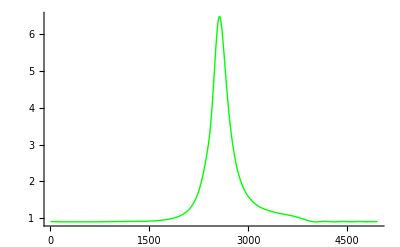

```mathematica
obr4=ListLinePlot[priemernehodnoty4stlpec+1.0335, PlotStyle->Green,PlotRange->All]
```

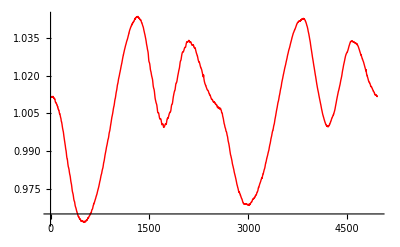

```mathematica
obr5=ListLinePlot[priemernehodnoty5stlpec,PlotStyle->Red]
```

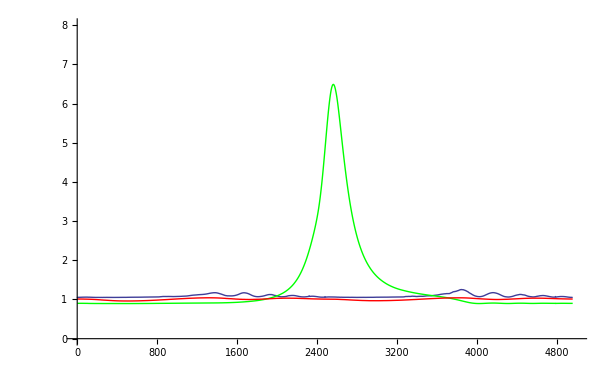

```mathematica
obrfinal=GraphicsGrid[{{obr3,obr4,obr5}},ImageSize->{1000,250}];
Show[{obr3,obr4,obr5},PlotRange->{{0,5000},{0,8}},AxesOrigin->{0,0}]
```

ešte exporty - ak by sme ich potrebovali do ineho programu

```mathematica
Export["final-"<>StringDrop[subor,-4]<>".pdf",obrfinal,"PDF"]
```

final-NG-1200-100SK-27BTDC.pdf

```mathematica
Export["tretistlpec-"<>subor<>".txt",priemernehodnoty3stlpec,"TEXT"]
Export["tretistlpec-"<>subor<>".xls",priemernehodnoty3stlpec,"XLS"]
```

tretistlpec-NG-1200-100SK-27BTDC.TXT.txt

tretistlpec-NG-1200-100SK-27BTDC.TXT.xls

```mathematica
Export["stvrtystlpec-"<>subor<>".txt",priemernehodnoty4stlpec,"TEXT"]
Export["stvrtystlpec-"<>subor<>".xls",priemernehodnoty4stlpec,"XLS"]
```

stvrtystlpec-NG-1200-100SK-27BTDC.TXT.txt

stvrtystlpec-NG-1200-100SK-27BTDC.TXT.xls

```mathematica
Export["piatystlpec-"<>subor<>".txt",priemernehodnoty5stlpec,"TEXT"]
Export["piatystlpec-"<>subor<>".xls",priemernehodnoty5stlpec,"XLS"]
```

piatystlpec-NG-1200-100SK-27BTDC.TXT.txt

piatystlpec-NG-1200-100SK-27BTDC.TXT.xls